# Prediction Model Using Wolfram Predict Function Running as a web-service at http://192.168.1.1 (NUS Networks Only)

## Importing Data

Data Import from Excel Sheet

```mathematica
datafile=FileNameJoin[{NotebookDirectory[],"obs_data_w.xlsx"}];
```

```mathematica
SemanticImport[datafile]
```

Dataset[<>]

Curating data

```mathematica
datasetnb = Import[datafile][[1]];
```

```mathematica
datasetnb =Drop[ datasetnb,1];
```

```mathematica
datalengthnb = Length[datasetnb];
```

## Assigning data to Attributes

```mathematica
Voltage = {};
CurrentDensity= {};
Temparature = {};
Uncertanity= {};
```

```mathematica
c1 = 0;
While[(c1 += 1) <datalengthnb ,
  {
    
    Voltage = Append[Voltage, datasetnb[[c1]][[2]]];
    Temparature = Append[Temparature, datasetnb[[c1]][[3]]];
    Uncertanity = Append[Uncertanity, datasetnb[[c1]][[4]]];
    CurrentDensity = Append[CurrentDensity, datasetnb[[c1]][[5]]];
    };
  ];
```

## Creating data-sets (training and test) for the model

Input set

```mathematica
inputset= Transpose[{Temparature,CurrentDensity}];
```

Complete set

```mathematica
completeset= {};
For[i=1,i<datalengthnb,i++,completeset = Append[completeset,inputset[[i]] -> Voltage[[i]]]];
```

Randomizing Complete set

```mathematica
CompletesetRandomized=completeset[[PermutationList@RandomPermutation@Length[completeset]]];
```

```mathematica
If[Length[completeset]==Length[CompletesetRandomized],FlagforMemoryleak=0,FlagforMemoryleak=1];
```

Creating training and test data-sets

```mathematica
TrainTestRatio = 0.8;
{TrainingSet,TestSet}=TakeDrop[CompletesetRandomized,Round[Length[CompletesetRandomized]*TrainTestRatio]];
```

## Running ‘Predict’ function using different prediction Methods

Linear Regression prediction Method

```mathematica
LinearPrediction= Predict[TrainingSet,Method->"LinearRegression"];
infolinearreg = Quiet[PredictorInformation[LinearPrediction]];
```

Neural Network prediction Method

```mathematica
NeuralNetwordPrediction = Quiet[Predict[TrainingSet,Method->"NeuralNetwork"]];		
infoNeuralNetwork = Quiet[PredictorInformation[NeuralNetwordPrediction]];
```

Nearest Neighbors prediction Method

```mathematica
NearestNeighborPrediction= Predict[TrainingSet,Method->"NearestNeighbors"];	
infoNN = Quiet[PredictorInformation[NearestNeighborPrediction]];
```

Random Forest prediction Method

```mathematica
RandomForestPrediction= Predict[TrainingSet,Method->"RandomForest"];
infoRF = Quiet[PredictorInformation[RandomForestPrediction]];
```

## Difference between actual and predicted values (Using Test Data)

Linear Regression prediction Method

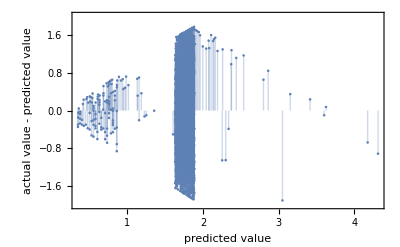

0.988698

```mathematica
PredictorMeasurements[LinearPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[LinearPrediction,TestSet,"StandardDeviation"]
```

Neural Network prediction Method

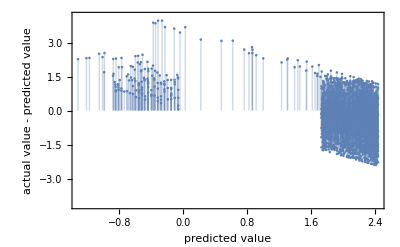

1.1708

```mathematica
PredictorMeasurements[NeuralNetwordPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[NeuralNetwordPrediction,TestSet,"StandardDeviation"]
```

Nearest Neighbors prediction Method

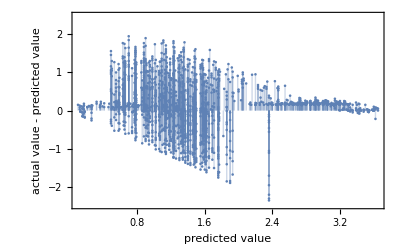

0.73113

```mathematica
PredictorMeasurements[NearestNeighborPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[NearestNeighborPrediction,TestSet,"StandardDeviation"]
```

Random Forest prediction Method

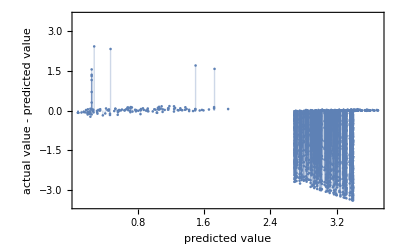

1.5846

```mathematica
PredictorMeasurements[RandomForestPrediction,TestSet,"ResidualPlot"]
PredictorMeasurements[RandomForestPrediction,TestSet,"StandardDeviation"]
```

## Predicting step voltage for 400 K

Linear Regression prediction Method

```mathematica
DesiredConditions = {140,0.1};
```

```mathematica
PredictedVonbyLRMethod = LinearPrediction[DesiredConditions]
```

1.91993

Neural Network prediction Method

```mathematica
PredictedVonbyNeurNetMethod = NeuralNetwordPrediction[DesiredConditions]
```

1.73579

Nearest Neighbors prediction Method

```mathematica
PredictedVonbyNearNeigMethod = NearestNeighborPrediction[DesiredConditions]
```

3.54

Random Forest prediction Method

```mathematica
PredictedVonbyRFMethod = RandomForestPrediction[DesiredConditions]
```

3.54043

```mathematica
(*Voltagetobeplotted = {};
Currenttobeplotted = {};
Temparaturetobeplotted = {};
c1 = 0;
While[(c1 += 1) <77,
  {
    
    Voltagetobeplotted = Append[Voltagetobeplotted, Voltage[[c1]]];
    Currenttobeplotted = Append[Currenttobeplotted, CurrentDensity[[c1]]];
Temparaturetobeplotted = Append[Temparaturetobeplotted, Temparature[[c1]]];
    };
  ];
toplotiv = Transpose[{Voltagetobeplotted,Currenttobeplotted}];
OutputValueplot =ListLinePlot[toplotiv,PlotRange->Automatic,PlotRange->{0,1}]*)
```